```mathematica
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../mathematica_utilities/mathematica_plot_options.nb"}]];
plot2Doption=Append[{PlotRange->All,PlotStyle->Red,Filling->Axis,GridLines->All,Joined->False},plot2Doption];
```

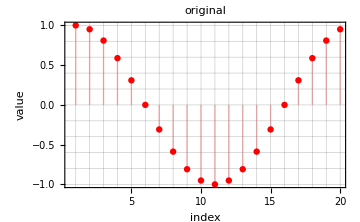

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_Fourier/./sample_original_cosWave.png

```mathematica
casename="cosWave";

(*cosWave*)
If[casename=="mathematica",
list={1.,1.,2.,2.,1.,1.,0.,0.};
]

n=20;
(*cosWave*)
If[casename=="cosWave",
list=Table[Cos[2π/n*i],{i,0,n-1,1}];
]

(*squareWave*)
If[casename=="squareWave",
list=Flatten[Table[{Table[-1,{i,1,n/2,1}],Table[1,{i,1,n/2,1}]},{i,1,2}]];
]

(*triangleWave*)
If[casename=="triangleWave",
halfWave=Join[Table[i,{i,-1,1,2/(n-1)}],Table[i,{i,1,-1,-2/(n-1)}][[2;;-2]]];
list=Flatten[{halfWave,halfWave}];
]

(*list=Table[Cos[2π/n*i]*Cos[5π/n*i],{i,0,n-1,1}];*)
fig=ListPlot[list,PlotLabel->"original",FrameLabel->{"index","value"},GridLines->All, Joined->False,Evaluate[plot2Doption]]
Export[FileNameJoin[{NotebookDirectory[],"./sample_original_"<>casename<>".png"}],fig]
```

```mathematica
num=30
(*list=Flatten@{Table[1,{i,1,num}],Table[2,{i,1,num}]}*)
(*list=Table[Cos[2π*i/num],{i,0,num-1}]*)
MyFourier[list_,n_]:=With[{len=Length[list]},Sum[list[[k+1]]*Exp[-I*n*2. π/len*k],{k,0,len-1}]/len];
Column[Fourier[list,FourierParameters->{-1,-1}],Frame->All]
Column[cn=Table[MyFourier[list,n],{n,0,Length[list]-1}],Frame->All]
```

30

0.
0.5
0.
0.
0.
2.16611×10^-17
0.
0.
0.
5.09346×10^-17
0.
-2.22045×10^-17
0.
3.78832×10^-17
0.
2.22045×10^-17
0.
5.43382×10^-19
0.
0.5

-1.66533×10^-17
0.5+1.66533×10^-17 ⅈ
5.55112×10^-17+4.44089×10^-17 ⅈ
1.66533×10^-17+6.10623×10^-17 ⅈ
4.996×10^-17+5.55112×10^-17 ⅈ
-4.54255×10^-17-2.77556×10^-17 ⅈ
8.88178×10^-17-3.33067×10^-17 ⅈ
-1.05471×10^-16+2.38698×10^-16 ⅈ
1.33227×10^-16-2.498×10^-16 ⅈ
2.16493×10^-16+3.77476×10^-16 ⅈ
0.-6.12323×10^-17 ⅈ
3.16414×10^-16+1.47105×10^-16 ⅈ
-6.71685×10^-16+3.71925×10^-16 ⅈ
-4.77396×10^-16-7.21645×10^-17 ⅈ
-2.13718×10^-16+2.10942×10^-16 ⅈ
5.74815×10^-16-1.16573×10^-16 ⅈ
-1.9984×10^-16+1.4988×10^-16 ⅈ
-4.38538×10^-16-8.88178×10^-17 ⅈ
8.32667×10^-17-4.77396×10^-16 ⅈ
0.5-3.96905×10^-16 ⅈ

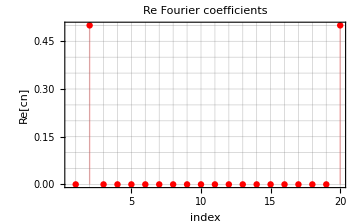

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_Fourier/./sample_Re_cn_cosWave.png

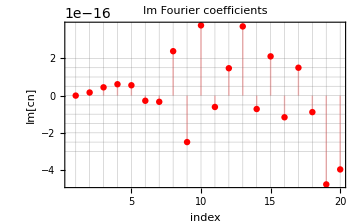

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_Fourier/./sample_Im_cn_cosWave.png

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_Fourier/./sample_ReIm_cn_cosWave.png

```mathematica
figRe=ListPlot[Re[cn],PlotLabel->"Re Fourier coefficients",FrameLabel->{"index","Re[cn]"},Evaluate[plot2Doption]]
Export[FileNameJoin[{NotebookDirectory[],"./sample_Re_cn_"<>casename<>".png"}],figRe]

figIm=ListPlot[Im[cn],PlotLabel->"Im Fourier coefficients",FrameLabel->{"index","Im[cn]"},Evaluate[plot2Doption]]
Export[FileNameJoin[{NotebookDirectory[],"./sample_Im_cn_"<>casename<>".png"}],figIm]

Export[FileNameJoin[{NotebookDirectory[],"./sample_ReIm_cn_"<>casename<>".png"}],Row[{figRe,figIm}]]
```

1.+1.4971×10^-16 ⅈ
0.951057-3.57173×10^-16 ⅈ
0.809017-8.24083×10^-16 ⅈ
0.587785+1.08881×10^-15 ⅈ
0.309017-2.8337×10^-16 ⅈ
-9.4369×10^-16-9.42513×10^-16 ⅈ
-0.309017+1.13417×10^-15 ⅈ
-0.587785+9.48974×10^-16 ⅈ
-0.809017+2.83613×10^-16 ⅈ
-0.951057-3.8964×10^-16 ⅈ
-1.-1.58491×10^-16 ⅈ
-0.951057+1.55026×10^-15 ⅈ
-0.809017-1.65437×10^-15 ⅈ
-0.587785+2.03189×10^-16 ⅈ
-0.309017-1.11857×10^-16 ⅈ
-2.22045×10^-16+2.17459×10^-15 ⅈ
0.309017+4.7661×10^-16 ⅈ
0.587785-1.3089×10^-15 ⅈ
0.809017+3.75747×10^-16 ⅈ
0.951057-2.35528×10^-15 ⅈ

1.+1.4971×10^-16 ⅈ
0.951057-4.44089×10^-16 ⅈ
0.809017-9.99201×10^-16 ⅈ
0.587785+1.16573×10^-15 ⅈ
0.309017-3.88578×10^-16 ⅈ
-9.90874×10^-16-8.88178×10^-16 ⅈ
-0.309017+9.99201×10^-16 ⅈ
-0.587785+8.88178×10^-16 ⅈ
-0.809017+2.77556×10^-16 ⅈ
-0.951057-4.16334×10^-16 ⅈ
-1.-1.27846×10^-16 ⅈ
-0.951057+1.55431×10^-15 ⅈ
-0.809017-1.4988×10^-15 ⅈ
-0.587785+2.77556×10^-16 ⅈ
-0.309017+0. ⅈ
-4.46865×10^-16+2.27596×10^-15 ⅈ
0.309017+4.996×10^-16 ⅈ
0.587785-1.33227×10^-15 ⅈ
0.809017+4.44089×10^-16 ⅈ
0.951057-2.35922×10^-15 ⅈ

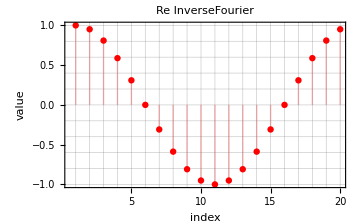

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_Fourier/./sample_Re_inv_cosWave.png

```mathematica
len=Length[list];
MyInverseFourier[list_,n_,max_ :(len-1)]:=With[{len=Length[list]},Sum[list[[k+1]]*Exp[I*n*2 π/len*k],{k,0,max}]/len];
Column[inv=InverseFourier[cn,FourierParameters->{-1,-1}],Frame->All]
Column[Table[MyInverseFourier[cn,n]*(Length[list]),{n,0,Length[list]-1,1}],Frame->All]

fig=ListPlot[Re[inv],PlotLabel->"Re InverseFourier",FrameLabel->{"index","value"},Evaluate[plot2Doption]]
Export[FileNameJoin[{NotebookDirectory[],"./sample_Re_inv_"<>casename<>".png"}],fig]
```

```mathematica
(*n-1->-1*)
(*n-2->-2*)
Floor[Length[cn]-1]
shift=If[EvenQ[(Length[cn]-1)/2],{(Length[cn]-1)/2,(Length[cn]-1)/2},{(Length[cn]-1+1)/2,(Length[cn]-1-1)/2}]
Do[Cn[i]=cn[[i+1]],{i,0,shift[[1]]}]
Do[Cn[-i]=cn[[Length[cn]+1-i]],{i,1,shift[[2]]}]
```

19

{10,9}

```mathematica
Column@Table[{i,Re@Cn[i]},{i,-shift[[2]],shift[[1]],1}]
```

{-9,3.16414×10^-16}
{-8,-6.71685×10^-16}
{-7,-4.77396×10^-16}
{-6,-2.13718×10^-16}
{-5,5.74815×10^-16}
{-4,-1.9984×10^-16}
{-3,-4.38538×10^-16}
{-2,8.32667×10^-17}
{-1,0.5}
{0,-1.66533×10^-17}
{1,0.5}
{2,5.55112×10^-17}
{3,1.66533×10^-17}
{4,4.996×10^-17}
{5,-4.54255×10^-17}
{6,8.88178×10^-17}
{7,-1.05471×10^-16}
{8,1.33227×10^-16}
{9,2.16493×10^-16}
{10,0.}

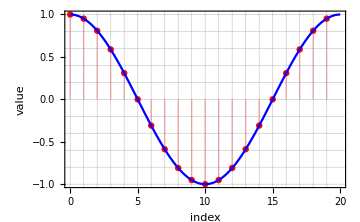

```mathematica
f[t_]:=With[{len=Length[list]},Sum[Cn[n]*Exp[I*n*2 π/len*t],{n,-shift[[2]],shift[[1]],1}]];
fig=Show[
ListPlot[Table[{i-1,list[[i]]},{i,1,Length[list],1}],FrameLabel->{"index","value"},Evaluate[plot2Doption]],
ListPlot[Table[{t,Re[f[t]]},{t,0,Length[list],0.1}],PlotStyle->Blue,Filling->None,Joined->True,Evaluate[plot2Doption]]
,PlotRange->All
]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"./sample_interpolation_"<>casename<>".png"}],fig]
```

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_Fourier/./sample_interpolation_cosWave.png

```mathematica
f[t_,expandmax_]:=With[{len=Length[list]},Sum[Cn[n]*Exp[I*n*2 π/len*t],{n,-expandmax,expandmax,1}]];
anim=Manipulate[
Show[
ListPlot[Table[{i-1,list[[i]]},{i,1,Length[list],1}],FrameLabel->{"index","value"},Evaluate[plot2Doption]],
ListPlot[Table[{t,Re[f[t,expandmax]]},{t,0,Length[list],0.1}],PlotStyle->Blue,Filling->None,Joined->True,Evaluate[plot2Doption]]
,PlotRange->All
,PlotLabel->expandmax
],{expandmax,1,Min[shift],1}]
```

ListPlot::nonopt: ListPlot[{},FrameLabel→{index,value},plot2Doption]における1の位置より後方にオプションが想定されます（plot2Doptionの代りに）．オプションは規則あるいは規則のリストでなければなりません．

ListPlot::nonopt: ListPlot[{{0.,Re[f[0.,1]]}},PlotStyle→RGBColor[0, 0, 1],Filling→None,Joined→True,plot2Doption]における1の位置より後方にオプションが想定されます（plot2Doptionの代りに）．オプションは規則あるいは規則のリストでなければなりません．

Show::gcomb: Show[ListPlot[{},FrameLabel→{index,value},plot2Doption],ListPlot[{{0.,Re[f[0.,1]]}},PlotStyle→RGBColor[0, 0, 1],Filling→None,Joined→True,plot2Doption],PlotRange→All,PlotLabel→1]のグラフィックスオブジェクトを組み合せることができませんでした．

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"./sample_convergence_"<>casename<>".gif"}],anim]
```

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_Fourier/./sample_convergence_cosWave.gif